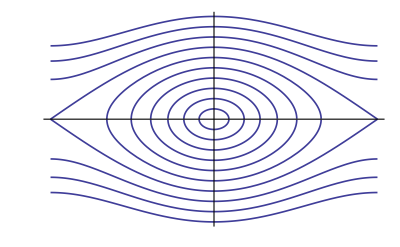

```mathematica
Plot[Table[{-Sqrt[k^2-Sin[t/2]^2],Sqrt[k^2-Sin[t/2]^2]},{k,1/7,10/7,1/7}],{t,-Pi,Pi},Ticks->None,PlotStyle->Thickness[0.003]]
```

```mathematica
ParametricPlot3D[Join[Table[{Cos[t],Sin[t],Sqrt[k^2-Sin[t/2]^2]},{k,1/7,9/7,1/7}],Table[{Cos[t],Sin[t],-Sqrt[k^2-Sin[t/2]^2]},{k,1/7,9/7,1/7}]],{t,-Pi,Pi},PlotStyle->Thick,Boxed->False,Axes->None,ColorFunction->Function[t,Hue[0,0,1.9*Cos[t]-1]]]
```

-Graphics3D-